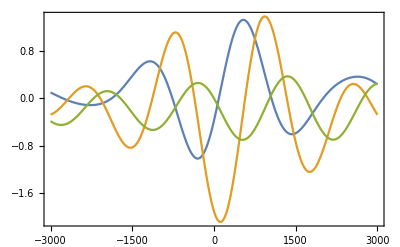

```mathematica
ClearAll["Global`*"]
t1=0.4*10^-3;
t2=3.5*10^-3;
γ1=300;
γ2=300;
Phie=Pi/2;
be=Pi/(4*t1);
(*Ω=2*x-1;*)
ω=Sqrt[Ω^2+be^2];
A11=(2*be^2*Cos[Phie]^2+(ω^2+Ω^2)*Cos[ω*t1]-be^2*Cosh[2*Phie]*Cos[ω*t1])/(2*ω^2);
A12=(be^2*Sin[2*Phie]^2*Sin[ω*t1/2]+Ω*ω*Sin[ω*t1])/(ω^2);
A13=(2*be*Ω*Cos[Phie]*Sin[ω*t1/2]^2-be*ω*Sin[Phie]*Sin[ω*t1])/(2*ω^2);
B11=(be^2*Sin[2*Phie]^2*Sin[ω*t1/2]-Ω*ω*Sin[ω*t1])/(ω^2);
B12=(2*be^2*Sin[Phie]^2+(ω^2+Ω^2)*Cos[ω*t1]+be^2*Cosh[2*Phie]*Cos[ω*t1])/(2*ω^2);
B13=(be*Ω*Sin[Phie]-be*Sin[Phie]*Sin[ω*t1]+be*ω*Cosh[Phie]*Sin[ω*t1])/(2*ω^2);
C11=(4*be*Ω*Cos[Phie]*Sin[ω*t1/2]^2+2*be*ω*Sin[Phie]*Sin[ω*t1])/(ω^2);
C12=(4*be*Ω*Sin[Phie]*Sin[ω*t1/2]^2-2*be*ω*Cos[Phie]*Sin[ω*t1])/(ω^2);
C13=(Ω^2+be^2*Cos[ω*t1])/(ω^2);
MRF={{A11,A12,A13},{B11,B12,B13},{C11,C12,C13}};
MRA={{Exp[-γ2*t2]*Cos[Ω*t2],Exp[-γ2*t2]*Sin[Ω*t2],0},{-Exp[-γ2*t2]*Sin[Ω*t2],Exp[-γ2*t2]*Cos[Ω*t2],0},{0,0,Exp[-γ1*t2]}};
R0={{0},{0},{-1}};
S=Dot[MRF,MRA];
Y=Dot[MRF,R0];
R=Dot[S,Y];//Simplify
Plot[R,{Ω,-3000,3000},PlotRange->All,Frame->True,Axes->False]
```